```mathematica
(*non-herm SSH OBC analytical solution*)
```

```mathematica
Ncell=60;
lst = Append[Flatten[ConstantArray[{v,w},Ncell-1]],v];
dlst = Flatten[ConstantArray[{u,-u},Ncell]];
h=DiagonalMatrix[lst,1]+DiagonalMatrix[lst,-1]+DiagonalMatrix[dlst];
ev =Eigensystem[h/.{v->2.0,w->1.0, u->1.0*I}];
```

```mathematica
evals=Reverse[Sort[ev[[1]]//Chop][[Ncell+1;;2Ncell]]];
```

```mathematica
f1=ListPlot[evals];
```

```mathematica
f2=Plot[N[Sqrt[v^2+w^2+u^2+2 v w Cos[x Pi/(Ncell+1)]]/.{v->2.0,w->1.0,u->1.0* I}],{x,1,Ncell}];
```

```mathematica
evals
```

{2.82748,2.82464,2.8199,2.81327,2.80476,2.79437,2.7821,2.76797,2.75198,2.73416,2.7145,2.69302,2.66974,2.64467,2.61783,2.58923,2.55891,2.52688,2.49315,2.45776,2.42073,2.38208,2.34184,2.30004,2.2567,2.21187,2.16556,2.11781,2.06865,2.01813,1.96626,1.9131,1.85867,1.80302,1.74618,1.68819,1.6291,1.56895,1.50778,1.44564,1.38256,1.3186,1.25381,1.18822,1.1219,1.05488,0.987221,0.918969,0.850176,0.780893,0.711171,0.641059,0.570607,0.499864,0.428874,0.357681,0.286327,0.214849,0.143281,0.0716547}

```mathematica
eval2//Chop
```

{2.82749,2.82468,2.81999,2.81344,2.80502,2.79473,2.7826,2.76862,2.75281,2.73517,2.71571,2.69446,2.67142,2.64661,2.62004,2.59174,2.56171,2.52999,2.49659,2.46154,2.42485,2.38656,2.34668,2.30525,2.26229,2.21783,2.17189,2.12452,2.07574,2.02558,1.97408,1.92128,1.86719,1.81187,1.75535,1.69766,1.63885,1.57895,1.51801,1.45605,1.39314,1.32929,1.26457,1.19901,1.13265,1.06555,0.997734,0.929258,0.860167,0.790505,0.720319,0.649655,0.578561,0.507083,0.435268,0.363165,0.290822,0.218285,0.145604,0.0728261}

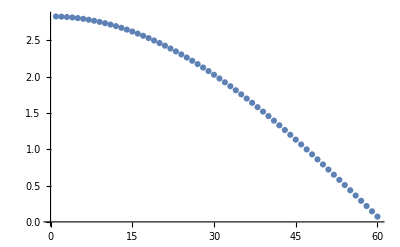

```mathematica
nLst = Range[Ncell];
eval2=N[Sqrt[v^2+w^2+u^2+2 v w Cos[nLst  Pi/(Ncell+1)]]/.{v->2.0,w->1.0,u->1.0* I}];
f2=ListPlot[eval2]
```

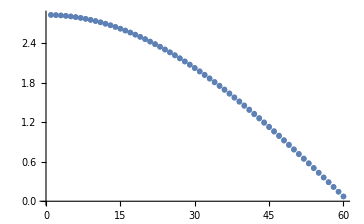

```mathematica
Show[{f1,f2}]
```

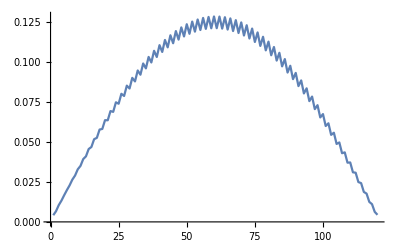

```mathematica
mode=1;
ListLinePlot[Transpose[Join[{Range[2Ncell]},{Re[ev[[2,mode]]]},1]],PlotRange->All]
```

```mathematica
Ncell=16;
lst = Append[Flatten[ConstantArray[{v,w},Ncell-1]],v];
dlst = Flatten[ConstantArray[{I u,-I u},Ncell]];
h=DiagonalMatrix[lst,1]+DiagonalMatrix[lst,-1]+DiagonalMatrix[dlst];
Eigenvalues[h/.{v->1.,w->1.,u->0.}]//Chop
```

{-1.99094,1.99094,-1.96386,1.96386,-1.91899,1.91899,1.85674,-1.85674,-1.77767,1.77767,1.68251,-1.68251,-1.57211,1.57211,1.44747,-1.44747,1.30972,-1.30972,-1.16011,1.16011,-1.,1.,0.83083,-0.83083,0.654136,-0.654136,0.471518,-0.471518,-0.28463,0.28463,0.0951638,-0.0951638}

```mathematica
ksol=NSolve[{(Exp[2I k(Ncell+1)]==(v+w Exp[I k])/(v+w Exp[-I k]))/.{v->1.8,w->1.3,u->0.5}},k];
ksol2 = ksol[[Ncell+2;;2Ncell+1]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{k→0.189471+0. ⅈ},{k→0.378925+0. ⅈ},{k→0.568346+0. ⅈ},{k→0.757712+0. ⅈ},{k→0.947001+0. ⅈ},{k→1.13618+0. ⅈ},{k→1.32521+0. ⅈ},{k→1.51403+0. ⅈ},{k→1.70256+0. ⅈ},{k→1.89068+0. ⅈ},{k→2.07818+0. ⅈ},{k→2.26471+0. ⅈ},{k→2.44969+0. ⅈ},{k→2.63199+0. ⅈ},{k→2.80955+0. ⅈ},{k→2.97947+0. ⅈ}}

```mathematica
Length[ksol]
```

34

```mathematica
N[Sqrt[v^2+w^2-u^2+2 v w Cos[k]]]/.{v->1.,w->1.,u->0.}/.ksol[[8]]
```

1.94188+0. ⅈ

```mathematica
eg=Eigensystem[h/.{v->1.8,w->1.3,u->0.5}]//Chop;
```

```mathematica
st=1;
eg[[1,st]]
vBench=eg[[2,st]]
```

3.04569

{0.0269738,0.0456411-0.00749272 ⅈ,0.0724633,0.0896486-0.0147173 ⅈ,0.115359,0.130447-0.0214151 ⅈ,0.154126,0.166577-0.0273464 ⅈ,0.187376,0.196745-0.0322989 ⅈ,0.21392,0.219871-0.0360954 ⅈ,0.232808,0.235127-0.0385999 ⅈ,0.243362,0.241968-0.0397229 ⅈ,0.245207,0.240148-0.0394242 ⅈ,0.238274,0.229733-0.0377143 ⅈ,0.222814,0.211095-0.0346546 ⅈ,0.199379,0.184901-0.0303546 ⅈ,0.168807,0.15209-0.0249681 ⅈ,0.132194,0.113835-0.0186879 ⅈ,0.0908486,0.0715061-0.0117389 ⅈ,0.046252,0.0266175-0.0043697 ⅈ}

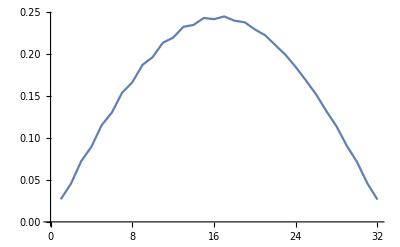

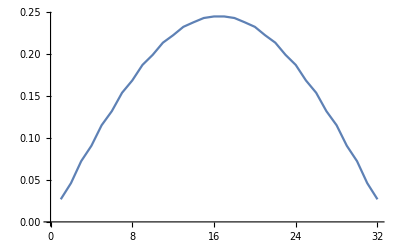

```mathematica
ListLinePlot[Re[eg[[2,st]]]]
ListLinePlot[Abs[eg[[2,st]]]]
```

```mathematica
vec=Flatten[Table[{a Exp[I k j]+b Exp[-I k j],c Exp[I k j]+d Exp[-I k j]},{j,1,Ncell}]];
Ek=2Sqrt[v^2+w^2-u^2+2 v w Cos[k]]; (*or, add an overall minus*)
vsol=vec/.{d->-c}/.{a->1,b->-(v+w Exp[I k])/(v+w Exp[-I k]),c->(-2I u+Ek)/(2(v+w Exp[-I k]))};
```

```mathematica
(-2I u+Ek)/(2(v+w Exp[I k]))/.{v->1.8,w->1.3,u->0.5}/.ksol[[8]]
```

0.933744-0.357942 ⅈ

```mathematica
Sqrt[(v+w Exp[-I k])/(v+w Exp[I k])]/.{v->1.8,w->1.3,u->0.5}/.ksol[[8]]
```

0.980181-0.198106 ⅈ

```mathematica
vnum=vsol/.{v->1.8,w->1.3,u->0.5}/.ksol[[8]];
(*vnum = vnum/vnum[[2]]*vBench[[2]]//Chop*)
```

```mathematica
vnum2=vsol/.{v->1.8,w->1.3,u->-0.5}/.ksol[[9]];
```

```mathematica
Conjugate[vnum2].vnum
```

1.25455×10^-14-3.38618×10^-15 ⅈ

```mathematica
vnum-vBench//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Ncell=16;
v0=1.8;
w0=1.3;
u0=0.5;

ksol=NSolve[{(Exp[2I k(Ncell+1)]==(v+w Exp[I k])/(v+w Exp[-I k]))/.{v->v0,w->w0,u->u0}},k];
ksol2 =k/. ksol[[Ncell+2;;2Ncell+1]];

vk=v+w Exp[-I k];
SuperStar[vk]=v+w Exp[I k];
vkp=v+w Exp[-I kp];
SuperStar[vkp]=v+w Exp[I kp];

vRp=Flatten[Table[{(vk ⅇ^(I k j)-SuperStar[vk] ⅇ^(-I k j))/(-I u+√(vk SuperStar[vk]-u^2)), ⅇ^(I k j)-ⅇ^(-I k j)},{j,1,Ncell}]];
vRm=Flatten[Table[{(vk ⅇ^(I k j)-SuperStar[vk] ⅇ^(-I k j))/(-I u-√(vk SuperStar[vk]-u^2)), ⅇ^(I k j)-ⅇ^(-I k j)},{j,1,Ncell}]];
vLp=Flatten[Table[{(vkp ⅇ^(I kp j)-SuperStar[vkp] ⅇ^(-I kp j))/(I u+√(vkp SuperStar[vkp]-u^2)), ⅇ^(I kp j)-ⅇ^(-I kp j)},{j,1,Ncell}]];
vLm=Flatten[Table[{(vkp ⅇ^(I kp j)-SuperStar[vkp] ⅇ^(-I kp j))/(I u-√(vkp SuperStar[vkp]-u^2)), ⅇ^(I kp j)-ⅇ^(-I kp j)},{j,1,Ncell}]];


tRp=Transpose[(vRp/.{v->v0,w->w0,u->u0,k->#})&/@ksol2];
tLp=Transpose[(vLp/.{v->v0,w->w0,u->u0,kp->#})&/@ksol2];
tRm=Transpose[(vRm/.{v->v0,w->w0,u->u0,k->#})&/@ksol2];
tLm=Transpose[(vLm/.{v->v0,w->w0,u->u0,kp->#})&/@ksol2];

tR=Join[tRp,tRm,2];
tL=Join[tLp,tLm,2];

(*Diagonal[ConjugateTranspose[tL].tR//Chop]*)

dfac=1/Sqrt[Diagonal[ConjugateTranspose[tL].tR//Chop]];
tR=tR.DiagonalMatrix[dfac];
tL=tL.DiagonalMatrix[Conjugate[dfac]];
Total[Abs[(ConjugateTranspose[tL].tR//Chop)-IdentityMatrix[2 Ncell]],2]

RFill=tR[[;;,Ncell+1;;2Ncell]];
LFill=tL[[;;,Ncell+1;;2Ncell]];

corr=RFill.ConjugateTranspose[LFill]//Chop;
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

6.10623×10^-15

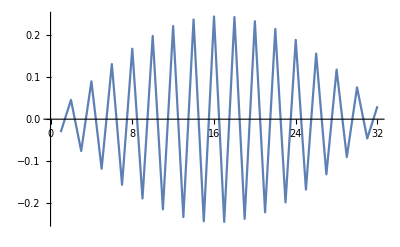

```mathematica
ListLinePlot[Im[tR[[;;,17]]]]
```

```mathematica
test=Transpose[Eigensystem[corr[[1;;24,1;;24]]][[2]]];
```

```mathematica
Transpose[test].test//Chop//MatrixForm
```

(0.906054-0.240736 ⅈ | 0.573526-0.307034 ⅈ | 0.0898174-0.0886055 ⅈ | 0.0323868-0.0718388 ⅈ | 0.0294326-0.00495365 ⅈ | 0.0640814-0.0133058 ⅈ | 0.0363509+0.0665624 ⅈ | 0.0516586+0.0472016 ⅈ | -1.87079×10^-6-1.62339×10^-6 ⅈ | -1.3881×10^-10-1.33995×10^-10 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.573526-0.307034 ⅈ | 0.145236+0.102401 ⅈ | -0.0255447-0.0201933 ⅈ | 0.00824517-0.0570557 ⅈ | 0.106104-0.120791 ⅈ | 0.207299-0.0423758 ⅈ | 0.0284385+0.105404 ⅈ | 0.152838+0.0155991 ⅈ | -2.0276×10^-6-1.18285×10^-6 ⅈ | -1.9054×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0898174-0.0886055 ⅈ | -0.0255447-0.0201933 ⅈ | 0.439379+0.252749 ⅈ | -0.175549+0.222264 ⅈ | -0.413917-0.00970564 ⅈ | -0.387721+0.0134607 ⅈ | -0.124495-0.291535 ⅈ | 0.094352-0.381772 ⅈ | -1.24045×10^-6-7.68212×10^-7 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0323868-0.0718388 ⅈ | 0.00824517-0.0570557 ⅈ | -0.175549+0.222264 ⅈ | 0.192949+0.0604489 ⅈ | 0.208489+0.154034 ⅈ | 0.359617-0.0136744 ⅈ | -0.257926+0.21374 ⅈ | 0.00659303-0.16733 ⅈ | -7.20713×10^-7-8.16185×10^-7 ⅈ | 0.+1.1065×10^-10 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0294326-0.00495365 ⅈ | 0.106104-0.120791 ⅈ | -0.413917-0.00970564 ⅈ | 0.208489+0.154034 ⅈ | 0.341963+0.00797931 ⅈ | 0.554485+0.0301126 ⅈ | -0.0469212+0.390586 ⅈ | 0.252737+0.210509 ⅈ | 3.22866×10^-7-1.35104×10^-7 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0640814-0.0133058 ⅈ | 0.207299-0.0423758 ⅈ | -0.387721+0.0134607 ⅈ | 0.359617-0.0136744 ⅈ | 0.554485+0.0301126 ⅈ | 0.210005+0.251428 ⅈ | -0.016874+0.157986 ⅈ | 0.349346-0.0310055 ⅈ | 1.50797×10^-7-7.74806×10^-7 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0363509+0.0665624 ⅈ | 0.0284385+0.105404 ⅈ | -0.124495-0.291535 ⅈ | -0.257926+0.21374 ⅈ | -0.0469212+0.390586 ⅈ | -0.016874+0.157986 ⅈ | 0.639936+0.314597 ⅈ | 0.666973+0.188761 ⅈ | 1.05919×10^-6-2.77832×10^-7 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0516586+0.0472016 ⅈ | 0.152838+0.0155991 ⅈ | 0.094352-0.381772 ⅈ | 0.00659303-0.16733 ⅈ | 0.252737+0.210509 ⅈ | 0.349346-0.0310055 ⅈ | 0.666973+0.188761 ⅈ | 0.751647-0.313382 ⅈ | 4.66699×10^-7-6.47857×10^-7 ⅈ | 1.51947×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.87079×10^-6-1.62339×10^-6 ⅈ | -2.0276×10^-6-1.18285×10^-6 ⅈ | -1.24045×10^-6-7.68212×10^-7 ⅈ | -7.20713×10^-7-8.16185×10^-7 ⅈ | 3.22866×10^-7-1.35104×10^-7 ⅈ | 1.50797×10^-7-7.74806×10^-7 ⅈ | 1.05919×10^-6-2.77832×10^-7 ⅈ | 4.66699×10^-7-6.47857×10^-7 ⅈ | 0.814138-0.185659 ⅈ | -3.09004×10^-10+1.34268×10^-10 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.3881×10^-10-1.33995×10^-10 ⅈ | -1.9054×10^-10 | 0 | 0.+1.1065×10^-10 ⅈ | 0 | 0 | 0 | 1.51947×10^-10 | -3.09004×10^-10+1.34268×10^-10 ⅈ | 0.718008+0.208708 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.631205-0.0926234 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.498424-0.334381 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.498424+0.334381 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.631205+0.0926234 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.718008-0.208708 ⅈ | 4.6456×10^-10+3.76429×10^-10 ⅈ | 0 | -1.39089×10^-10-2.62829×10^-10 ⅈ | 0.+1.55905×10^-10 ⅈ | 0.+1.46965×10^-10 ⅈ | 0.-2.3144×10^-10 ⅈ | 0 | 0 | 1.36385×10^-10-1.03617×10^-10 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.6456×10^-10+3.76429×10^-10 ⅈ | 0.814138+0.185659 ⅈ | 7.52108×10^-7-2.24535×10^-7 ⅈ | -8.93116×10^-8-6.54001×10^-8 ⅈ | 4.36915×10^-8+2.7485×10^-7 ⅈ | 2.43791×10^-7-5.44468×10^-7 ⅈ | 9.05286×10^-7-1.36614×10^-7 ⅈ | 2.53817×10^-7+4.12987×10^-7 ⅈ | -2.60091×10^-7-6.47089×10^-7 ⅈ | 7.12264×10^-7-9.37056×10^-8 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.52108×10^-7-2.24535×10^-7 ⅈ | 0.756317+0.405796 ⅈ | 0.0379535-0.103596 ⅈ | -0.00520545+0.0414017 ⅈ | -0.0154659-0.250746 ⅈ | 0.0464495+0.263365 ⅈ | -0.0184706+0.0187155 ⅈ | -0.0144085+0.0333816 ⅈ | -0.011882+0.0999494 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.39089×10^-10-2.62829×10^-10 ⅈ | -8.93116×10^-8-6.54001×10^-8 ⅈ | 0.0379535-0.103596 ⅈ | 0.732747+0.283765 ⅈ | -0.499087-0.163056 ⅈ | 0.0068832-0.0212858 ⅈ | -0.0144208+0.0702524 ⅈ | 0.157525-0.198666 ⅈ | -0.155273+0.228682 ⅈ | 0.326931+0.0620179 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+1.55905×10^-10 ⅈ | 4.36915×10^-8+2.7485×10^-7 ⅈ | -0.00520545+0.0414017 ⅈ | -0.499087-0.163056 ⅈ | 0.679538-0.092854 ⅈ | -0.0509904+0.197179 ⅈ | -0.00263688-0.136866 ⅈ | 0.22414-0.0124222 ⅈ | 0.137931-0.298888 ⅈ | -0.318558-0.144616 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+1.46965×10^-10 ⅈ | 2.43791×10^-7-5.44468×10^-7 ⅈ | -0.0154659-0.250746 ⅈ | 0.0068832-0.0212858 ⅈ | -0.0509904+0.197179 ⅈ | 0.601252-0.153914 ⅈ | -0.37791+0.682531 ⅈ | 0.00503383+0.231057 ⅈ | -0.0928564+0.0601234 ⅈ | -0.0532553+0.49602 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.-2.3144×10^-10 ⅈ | 9.05286×10^-7-1.36614×10^-7 ⅈ | 0.0464495+0.263365 ⅈ | -0.0144208+0.0702524 ⅈ | -0.00263688-0.136866 ⅈ | -0.37791+0.682531 ⅈ | 0.0977557-0.145189 ⅈ | 0.154236-0.0794574 ⅈ | 0.100645-0.0152833 ⅈ | 0.127742-0.00303161 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.53817×10^-7+4.12987×10^-7 ⅈ | -0.0184706+0.0187155 ⅈ | 0.157525-0.198666 ⅈ | 0.22414-0.0124222 ⅈ | 0.00503383+0.231057 ⅈ | 0.154236-0.0794574 ⅈ | 0.554471+0.23044 ⅈ | -0.233583-0.0500013 ⅈ | 0.140071+0.077273 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.60091×10^-7-6.47089×10^-7 ⅈ | -0.0144085+0.0333816 ⅈ | -0.155273+0.228682 ⅈ | 0.137931-0.298888 ⅈ | -0.0928564+0.0601234 ⅈ | 0.100645-0.0152833 ⅈ | -0.233583-0.0500013 ⅈ | 0.430525-0.453272 ⅈ | -0.161682-0.221455 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.36385×10^-10-1.03617×10^-10 ⅈ | 7.12264×10^-7-9.37056×10^-8 ⅈ | -0.011882+0.0999494 ⅈ | 0.326931+0.0620179 ⅈ | -0.318558-0.144616 ⅈ | -0.0532553+0.49602 ⅈ | 0.127742-0.00303161 ⅈ | 0.140071+0.077273 ⅈ | -0.161682-0.221455 ⅈ | 0.361433+0.365043 ⅈ)

```mathematica
Eigenvalues[corr[[1;;24,1;;24]]]//MatrixForm//Chop
```

(1.
1.
1.
1.
1.
1.
1.
1.
1.
1.-3.66183×10^-7 ⅈ
0.999732-0.000385165 ⅈ
0.961079-0.0872302 ⅈ
0.0389209-0.0872302 ⅈ
0.000267954-0.000385165 ⅈ
3.90604×10^-7-3.66183×10^-7 ⅈ
0
0
0
0
0
0
0
0
0)

```mathematica
test ={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
Eigensystem[test]
```

{{1/2 (5+√33),1/2 (5-√33)},{{1/6 (-3+√33),1},{1/6 (-3-√33),1}}}

```mathematica
Eigensystem[test][[2]]//MatrixForm
```

(1/6 (-3+√33) | 1
1/6 (-3-√33) | 1)